# Obtención de estrellas hibridas

```mathematica
Quit[]
```

### Covariant Equations

```mathematica
<<xAct`xTensor`
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;

SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)

$CommuteCovDsOnScalars=True;

Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
DefManifold[M4,4,IndexRange[a,n]]
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]

(*Defining the scalar field *)
DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensor[PhiC[],M4,PrintAs->"φ^*"]

(* We defining X and other constant
Definiendo X=▽_a ϕ ▽^a ϕ^* *)
DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],CD[a][Phi[]]CD[-a][PhiC[]]]
```

(▽_a φ^*) (▽^a φ)

```mathematica
DefConstantSymbol[ka, PrintAs ->"k"]
DefConstantSymbol[aB, PrintAs ->"α_B"]
DefConstantSymbol[mS, PrintAs ->"m"]
```

```mathematica
(* Einstein Klein-Gordon dynamic action *)
(*k= c^4/(16Gπ), β tienen unidades, las α no*)
LRG=ka  RicciScalarCD[];
Lϕ =-aB (X[]+mS^2*Phi[]*PhiC[]);
Ltot=LRG+Lϕ
```

k R[▽]-α_B (m^2 φ φ^*+(▽_a φ^*) (▽^a φ))

```mathematica
Print["Computing the variations as:1/(√-g)(δ (SqrtBox[-g] L))/δg^ab", "We used VarD: VarD[g[a,b],cd][L] that returns δL/δg^ab while integrating by parts with respect to the covariant derivative cd."]
```

Computing the variations as:1/(√-g)(δ (SqrtBox[-g] L))/δg^abWe used VarD: VarD[g[a,b],cd][L] that returns δL/δg^ab while integrating by parts with respect to the covariant derivative cd.

```mathematica
(*ϕ*)
Print["GR contribution:"]
EqϕRG =1/Sqrt[-Detmetric[]] VarD[PhiC[],CD][Sqrt[-Detmetric[]]LRG]//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical//Simplification

Print["Klein-Gordon Equation:"]
KG =1/Sqrt[-Detmetric[]] VarD[PhiC[],CD][Sqrt[-Detmetric[]]Lϕ]//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical//Simplification

Print["Scalar Field Equation:"]
Eqϕ=EqϕRG+KG==0
```

GR contribution:

0

Klein-Gordon Equation:

α_B (-m^2 φ+▽_a▽^a φ)

Scalar Field Equation:

α_B (-m^2 φ+▽_a▽^a φ)==0

```mathematica
(*g^ab Notice that by simplicity we use VarL*)
Print["GR equation:"]
EqRG =VarL[metric[a,b],CD][LRG]//ContractMetric//ToCanonical//RicciToEinstein//Simplification

Print["Scalar Field contribution:"]
Eqrϕ =VarL[metric[a,b],CD][Lϕ]//ContractMetric//ToCanonical//RicciToEinstein//Simplification

Print["Field Equations:"]
EqField=EqRG+Eqrϕ
```

GR equation:

k G[▽] |   |  
a | b

Scalar Field contribution:

1/2 α_B (-(▽_a φ^*) (▽_b φ)-(▽_a φ) (▽_b φ^*)+g |   |  
a | b (m^2 φ φ^*+(▽_c φ^*) (▽^c φ)))

Field Equations:

k G[▽] |   |  
a | b+1/2 α_B (-(▽_a φ^*) (▽_b φ)-(▽_a φ) (▽_b φ^*)+g |   |  
a | b (m^2 φ φ^*+(▽_c φ^*) (▽^c φ)))

```mathematica
(*Notice that the field contribution is -Subscript[T, μν]^(ϕ)/2*)
Tϕ = -2VarL[metric[a,b],CD][Lϕ]//Simplify;
Print["T_ab^(ϕ)=-2/(√-g)(δ (SqrtBox[-g] SuperscriptBox[L, (ϕ)]))/δg^ab=",Tϕ//ScreenDollarIndices]
```

T_ab^(ϕ)=-2/(√-g)(δ (SqrtBox[-g] SuperscriptBox[L, (ϕ)]))/δg^ab=α_B ((▽_a φ^*) (▽_b φ)+(▽_a φ) (▽_b φ^*)-g |   |  
a | b (m^2 φ φ^*+(▽_c φ^*) (▽^c φ)))

```mathematica
Print["The field equations are: \n", "G_ab=1/(2  k)(T_ab+T_ab^(ϕ))"](*check using: https://physics.stackexchange.com/questions/74834/the-einstein-klein-gordon-ekg-equations*)
```

The field equations are: 
G_ab=1/(2  k)(T_ab+T_ab^(ϕ))

#### Defining the metric-coord

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],Φ[]},ChartColor->Brown] (*coordinate system*)
```

```mathematica
(*metric field*)
DefScalarFunction[NN,PrintAs->"N"]
DefScalarFunction[gg,PrintAs->"g"]
(*DefScalarFunction/@{NN, gg};*)

$Assumptions={r[]>0,θ[]>0,θ[]<π,Φ[]>0,Φ[]<2π};
MatrixForm[metricarray={{-( NN[r[]])^2,0,0,0},{0,gg[r[]]^2,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]

(*using the new methodology *)
metric2=CTensor[metricarray,{-esf,-esf}];
Invmetric2 =Inv[metric2];
```

(-N[r]^2 | 0 | 0 | 0
0 | g[r]^2 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

```mathematica
(*definiendo la derivada covariante y parcial en esta métrica*)
cd=CovDOfMetric[metric2];
pd=PDOfBasis[esf];
```

```mathematica
(*Calculando algunas cantidades con esta métrica*)
Riccicd = Ricci[cd];
RicciScalarcd=RicciScalar[cd];
Riemanncd=Riemann[cd];
Einsteincd=Einstein[cd];
```

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]
```

```mathematica
(* 
creando reglas para evaluar en las ecuaciones covariantes
*)
rules={
metric[a_?DownIndexQ,b_?DownIndexQ]:>metric2[a,b],
metric[a_?UpIndexQ,b_?UpIndexQ]:>Invmetric2[a,b],
Det[g[]]->Det[metricarray],
CD[a_?DownIndexQ]:>cd[a],
PD[a_?DownIndexQ]:>pd[a],
RicciCD[a_?DownIndexQ,b_?DownIndexQ]:>Riccicd[a,b],
RicciScalarCD[]:>RicciScalarcd[],
RiemannCD[a_?DownIndexQ,b_?DownIndexQ,c_?DownIndexQ,d_?DownIndexQ]:>Riemanncd[a,b,c,d],
EinsteinCD[a_?DownIndexQ,b_?DownIndexQ]:>Einsteincd[a,b],
Phi[]:>φ[r[]]Exp[ⅈ w t[]],
PhiC[]:>φ[r[]]Exp[-ⅈ w t[]]
};
```

```mathematica
(*Ecuaciones en simetría esférica*)
(* Scalar field*)
Ecuϕ2 = Eqϕ[[1]]//SeparateMetric[]//Expand;
listϕ2=Ecuϕ2//.rules//FromBasisExpand//ToCCanonical//Simplify;
resultϕ=Collect[listϕ2,{aB},Simplify]==0;
eqPhi=Last@Solve[resultϕ, ϕ''[r]]//FullSimplify
```

{ϕ''[r]→g[r]^2 (m^2-w^2/N[r]^2) ϕ[r]+(g'[r] ϕ'[r])/g[r]-((2 N[r]+r N'[r]) ϕ'[r])/(N[r] r)}

```mathematica
(*Ecuación de movimiento para las componentes de la métrica
Recordar: Subscript[G, ab]=1/(2k)(Subscript[T, ab]+Subscript[T, ab]^(ϕ))
*)
EqRG2=EqRG/ka//SeparateMetric[]//Expand;
resultMetrGR=EqRG2//.rules//FromBasisExpand//ToCCanonical;
ResultMetrGR = Head[resultMetrGR]
```

CTensor[{{(N[r]^2 (-g[r]+g[r]^3+2 r g'[r]))/(g[r]^3 r^2),0,0,0},{0,(N[r]-g[r]^2 N[r]+2 r N'[r])/(N[r] r^2),0,0},{0,0,(r (-N[r] g'[r]-r g'[r] N'[r]+g[r] (N'[r]+r N''[r])))/(g[r]^3 N[r]),0},{0,0,0,(r Sin[θ]^2 (-N[r] g'[r]-r g'[r] N'[r]+g[r] (N'[r]+r N''[r])))/(g[r]^3 N[r])}},{-esf,-esf},0]

```mathematica
TϕEq=Tϕ//SeparateMetric[]//Expand;
resultMetrTϕEq=TϕEq//.rules//FromBasisExpand//ToCCanonical//FullSimplify;
ResultMetrTϕEq= Head[resultMetrTϕEq]
```

CTensor[{{α_B ((w^2+m^2 N[r]^2) ϕ[r]^2+(N[r]^2 ϕ'[r]^2)/g[r]^2),0,0,0},{0,α_B ((g[r]^2 (w^2-m^2 N[r]^2) ϕ[r]^2)/N[r]^2+ϕ'[r]^2),0,0},{0,0,α_B r^2 ((-m^2+w^2/N[r]^2) ϕ[r]^2-ϕ'[r]^2/g[r]^2),0},{0,0,0,α_B r^2 Sin[θ]^2 ((-m^2+w^2/N[r]^2) ϕ[r]^2-ϕ'[r]^2/g[r]^2)}},{-esf,-esf},0]

```mathematica
(*Energy Momemtum tensor*)
```

```mathematica
DefTensor[u[a],M4,PrintAs->"u"]
ClearAll[Uup,Udown]

(*restframe*)
Uup=CTensor[{1/(NN[r[]]),0,0,0},{esf}];  (*U^0>0 velocity to be future directed*)
Udown=CTensor[{-NN[r[]],0,0,0},{-esf}];  

Urules={
u[a_?DownIndexQ]:>Udown[a],
u[a_?UpIndexQ]:>Uup[a]
};

(* checking *)
metric[a,b]u[-b]/.rules/.Urules
metric2[-a,-b]u[b]/.rules/.Urules
metric2[-a,-b]u[a]u[b]/.rules/.Urules
```

1/N[r]
0
0
0 | a

-N[r]
0
0
0 |  
a

-1

```mathematica
(*Energy Momentum tensor for a perfect fluid*)
DefTensor[T[a,b],M4,PrintAs->"T"]

DefScalarFunction[den,PrintAs->"ρ"]
DefScalarFunction[pres,PrintAs->"P"]
DefConstantSymbol[epsil,PrintAs->"ϵ"]
```

```mathematica
IndexSet[T[a_,b_],(den[r[]](1+epsil)+pres[r[]])u[a]u[b]+pres[r[]]metric[a,b]]
```

g | a | b
  |   P[r]+((1+ϵ) ρ[r]+P[r]) u | a
  u | b

```mathematica
ruldelta=delta[b_?DownIndexQ, a_?UpIndexQ]:>metric2[b,-c] Invmetric2[c,a]
```

δ | UnderBar[b̲] | UnderBar[a̲]
  |  :>metric2[b,-c] Invmetric2[c,a]

```mathematica
EMup=T[a,b]/.rules/.Urules//Simplify
Emmixed=T[a,-b]/.rules/.Urules/.ruldelta//Simplify
EMdown=T[-a,-b]/.rules/.Urules//Simplify
tensorT=Head[T[-a,-b]/.rules/.Urules//Simplify]
```

((1+ϵ) ρ[r])/N[r]^2 | 0 | 0 | 0
0 | P[r]/g[r]^2 | 0 | 0
0 | 0 | P[r]/r^2 | 0
0 | 0 | 0 | (Csc[θ]^2 P[r])/r^2 | a | b
  |

-((1+ϵ) ρ[r]) | 0 | 0 | 0
0 | P[r] | 0 | 0
0 | 0 | P[r] | 0
0 | 0 | 0 | P[r] | a |  
  | b

(1+ϵ) ρ[r] N[r]^2 | 0 | 0 | 0
0 | g[r]^2 P[r] | 0 | 0
0 | 0 | P[r] r^2 | 0
0 | 0 | 0 | P[r] r^2 Sin[θ]^2 |   |  
a | b

CTensor[{{(1+ϵ) ρ[r] N[r]^2,0,0,0},{0,g[r]^2 P[r],0,0},{0,0,P[r] r^2,0},{0,0,0,P[r] r^2 Sin[θ]^2}},{-esf,-esf},0]

The field equations are: \nG_ab+GB_ab/k=1/(2  k)(T_ab+T_ab^(ϕ))

```mathematica
Print["Componente 00"]
eq00=Collect[ResultMetrGR[[1,1,1]]==1/(2ka)(tensorT[[1,1,1]]+ResultMetrTϕEq[[1,1,1]]),{aB}, FullSimplify]

Print["Componente 11"]
eq11=Collect[ResultMetrGR[[1,2,2]]==1/(2ka)(tensorT[[1,2,2]]+ResultMetrTϕEq[[1,2,2]]),{aB}, FullSimplify]
```

Componente 00

(N[r]^2 (-g[r]+g[r]^3+2 r g'[r]))/(g[r]^3 r^2)==((1+ϵ) ρ[r] N[r]^2)/(2 k)+(α_B ((w^2+m^2 N[r]^2) ϕ[r]^2+(N[r]^2 ϕ'[r]^2)/g[r]^2))/(2 k)

Componente 11

(N[r]-g[r]^2 N[r]+2 r N'[r])/(N[r] r^2)==(g[r]^2 P[r])/(2 k)+(α_B ((g[r]^2 (w^2-m^2 N[r]^2) ϕ[r]^2)/N[r]^2+ϕ'[r]^2))/(2 k)

```mathematica
(*Metric equations*)
Eqg=Last@Collect[Solve[eq00, g'[r]],aB,FullSimplify]
EqN=Last@Collect[Solve[eq11,  N'[r]],aB,FullSimplify]
```

{g'[r]→(2 k g[r]+g[r]^3 (-2 k+(1+ϵ) ρ[r] r^2))/(4 k r)+(α_B g[r] r (g[r]^2 (w^2+m^2 N[r]^2) ϕ[r]^2+N[r]^2 ϕ'[r]^2))/(4 k N[r]^2)}

{N'[r]→(N[r] (-2 k+g[r]^2 (2 k+P[r] r^2)))/(4 k r)+(α_B r (g[r]^2 (w^2-m^2 N[r]^2) ϕ[r]^2+N[r]^2 ϕ'[r]^2))/(4 k N[r])}

```mathematica
(*Ecuación de conservación*)
```

```mathematica
conserv=CD[-a][T[a,b]];
Eqconserv=conserv//.rules//.Urules//FromBasisExpand//ToCCanonical;
Eqconserv=Head[Eqconserv];
Dp=Solve[Eqconserv[[1,2]]==0,P'[r]][[1,1]]/.Rule->Equal//Simplify
```

P'[r]==-(((1+ϵ) ρ[r]+P[r]) N'[r])/N[r]

Finalmente tendremos que:

```mathematica
ePhi=Last@eqPhi/.{r[]-> r, mS-> m,ka->Mp^2/(16 π)}/.Rule->Equal
eqg=Last@Eqg/.{r[]-> r, mS-> m,ka->Mp^2/(16π)}/.Rule->Equal
eqN=Last@EqN/.{r[]-> r, mS-> m,ka->Mp^2/(16π)}/.Rule->Equal
eqP=Dp/.{r[]-> r, mS-> m,ka->Mp^2/(16 π)}/.Rule->Equal
```

ϕ''[r]==g[r]^2 (m^2-w^2/N[r]^2) ϕ[r]+(g'[r] ϕ'[r])/g[r]-((2 N[r]+r N'[r]) ϕ'[r])/(r N[r])

g'[r]==(4 π ((Mp^2 g[r])/(8 π)+(-Mp^2/(8 π)+(1+ϵ) r^2 ρ[r]) g[r]^3))/(Mp^2 r)+(4 α_B π r g[r] (g[r]^2 (w^2+m^2 N[r]^2) ϕ[r]^2+N[r]^2 ϕ'[r]^2))/(Mp^2 N[r]^2)

N'[r]==(4 π N[r] (-Mp^2/(8 π)+g[r]^2 (Mp^2/(8 π)+r^2 P[r])))/(Mp^2 r)+(4 α_B π r (g[r]^2 (w^2-m^2 N[r]^2) ϕ[r]^2+N[r]^2 ϕ'[r]^2))/(Mp^2 N[r])

P'[r]==-(((1+ϵ) ρ[r]+P[r]) N'[r])/N[r]

### Numerical Solutions

```mathematica
Quit[]
```

```mathematica
system={
ϕ''[r]==g[r]^2 (m^2-w^2/N[r]^2) ϕ[r]+(g'[r] ϕ'[r])/g[r]-((2 N[r]+r N'[r]) ϕ'[r])/(r N[r]),g'[r]==(4 π ((Mp^2 g[r])/(8 π)+(-Mp^2/(8 π)+(1+ϵ) r^2 ρ[r]) g[r]^3))/(Mp^2 r)+(4 Subscript[α, B] π r g[r] (g[r]^2 (w^2+m^2 N[r]^2) ϕ[r]^2+N[r]^2 ϕ'[r]^2))/(Mp^2 N[r]^2),N'[r]==(4 π N[r] (-Mp^2/(8 π)+g[r]^2 (Mp^2/(8 π)+r^2 P[r])))/(Mp^2 r)+(4 Subscript[α, B] π r (g[r]^2 (w^2-m^2 N[r]^2) ϕ[r]^2+N[r]^2 ϕ'[r]^2))/(Mp^2 N[r]),
P'[r]==-(((1+ϵ) ρ[r]+P[r]) N'[r])/N[r]}
```

{φ''[r]==gg[r]^2 (m^2-w^2/NN[r]^2) φ[r]+(gg'[r] φ'[r])/gg[r]-((2 NN[r]+r NN'[r]) φ'[r])/(r NN[r]),gg'[r]==(4 π ((Mp^2 gg[r])/(8 π)+(-Mp^2/(8 π)+(1+epsil) r^2 den[r]) gg[r]^3))/(Mp^2 r)+(4 aB π r gg[r] (gg[r]^2 (w^2+m^2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/(Mp^2 NN[r]^2),NN'[r]==(4 π NN[r] (-Mp^2/(8 π)+gg[r]^2 (Mp^2/(8 π)+r^2 pres[r])))/(Mp^2 r)+(4 aB π r (gg[r]^2 (w^2-m^2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/(Mp^2 NN[r]),pres'[r]==-(((1+epsil) den[r]+pres[r]) NN'[r])/NN[r]}

### Introducing the dimensionless variables

```mathematica
newVar={r-> x/m,pres[r]->m^2 Mp^2 P,den[r]->m^2 Mp^2 ρ,w-> ω m, ϕ[r]-> σ[x] Mp,ϕ'[r]->  D[σ[x],x]m Mp,ϕ''[r]-> D[σ[x],{x,2}] m^2 Mp,NN[r]-> NN[x],NN'[r]-> D[NN[x],x]m, NN''[r]-> D[NN[x],{x,2}] m^2,gg[r]-> gg[x],gg'[r]-> gg'[x]m,L3-> Λ Mp^(1/3)m^(2/3)};
```

```mathematica
(*N'*)
mdN=system[[3,2]]/m/.newVar//Simplify;
mdNU=system[[3,2]]/.{m->1, Mp->1,r-> x, w-> ω, pres[r]->P, L3-> Λ, ϕ[r]-> σ[x],ϕ'[r]->  D[σ[x],x],ϕ''[r]-> D[σ[x],{x,2}]};
mdNU-mdN//Simplify
```

0

```mathematica
(*g'*)
mdg=system[[2,2]]/m/.newVar//Simplify;
mdgU=system[[2,2]]/.{m->1, Mp->1,r-> x, w-> ω, pres[r]->P,den[r]->ρ, L3-> Λ, ϕ[r]-> σ[x],ϕ'[r]->  D[σ[x],x],ϕ''[r]-> D[σ[x],{x,2}]};
mdgU-mdg//Simplify
```

0

```mathematica
(*ϕ''*)
mddϕ=system[[1,2]]/(m^2 Mp)/.newVar//Simplify;
mddϕU=system[[1,2]]/.{m->1, Mp->1,r-> x, w-> ω, pres[r]->P,den[r]->ρ, L3-> Λ, ϕ[r]-> σ[x],ϕ'[r]->  D[σ[x],x],ϕ''[r]-> D[σ[x],{x,2}]};
mddϕU-mddϕ//Simplify
```

0

```mathematica
(*P*)
mdp=system[[4,2]]/(m m^2 Mp^2)/.newVar//Simplify;
mdpU=system[[4,2]]/.{m->1, Mp->1,r-> x, w-> ω, pres[r]->P,den[r]->ρ, L3-> Λ, ϕ[r]-> σ[x],ϕ'[r]->  D[σ[x],x],ϕ''[r]-> D[σ[x],{x,2}]};
mdpU-mdp//Simplify
```

0

```mathematica
(*correcta la adimensionalización. Por tanto podemos tomar m=1, Mp=1 y usar el mismo sistema*)
```

### Solving the System of equation

#### estrella de bosones

```mathematica
system1=system/.{ pres[r]->0,den[r]-> 0, epsil->0}/.{m->1, Mp->1}
```

{φ''[r]==gg[r]^2 (2-w^2/NN[r]^2) φ[r]+(gg'[r] φ'[r])/gg[r]-((2 NN[r]+r NN'[r]) φ'[r])/(r NN[r]),gg'[r]==(4 π (gg[r]/(8 π)-gg[r]^3/(8 π)))/r+(2 aB π r gg[r] (gg[r]^2 (w^2+2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/NN[r]^2,NN'[r]==(4 π (-1/(8 π)+gg[r]^2/(8 π)) NN[r])/r+(2 aB π r (gg[r]^2 (w^2-2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/NN[r],P'[r]==0}

```mathematica
(*near of origin*)
eq1=Numerator@Factor@(system1[[1,1]]-system1[[1,2]]);
eq2=Numerator@Factor@(system1[[2,1]]-system1[[2,2]]);
eq3=Numerator@Factor@(system1[[3,1]]-system1[[3,2]]);

(*expandiendo*)
ser1=Series[Numerator[eq1],{r, 0,2}]//Factor//Normal;
ser2=Series[Numerator[eq2],{r, 0,2}]//Factor//Normal;
ser3=Series[Numerator[eq3],{r, 0,2}]//Factor//Normal;
```

```mathematica
(*orden cero*)
ordeq10= Coefficient[ser1,r,0]//Simplify;
ordeq20= Coefficient[ser2,r,0]//Simplify;
ordeq30= Coefficient[ser3,r,0]//Simplify;

(*orden 1*)
ordeq11= Coefficient[ser1,r,1]//Simplify;
ordeq21= Coefficient[ser2,r,1]//Simplify;
ordeq31= Coefficient[ser3,r,1]//Simplify;
```

```mathematica
dphi=Last@Solve[ordeq10==0,φ'[0]]
gg0=Last@Solve[ordeq20==0/.dphi,gg[0]]
ddphi=Last@Solve[ordeq11==0/.dphi/.gg0,φ''[0]]
dgg0=Last@Solve[ordeq21==0/.dphi/.gg0/.ddphi,gg'[0]]
dN=Last@Solve[ordeq31==0/.dphi/.gg0/.ddphi/.dgg0,NN'[0]]
```

{φ'[0]→0}

{gg[0]→1}

{φ''[0]→(-w^2 φ[0]+2 NN[0]^2 φ[0])/(3 NN[0]^2)}

{gg'[0]→0}

{NN'[0]→0}

```mathematica
SNO=Series[NN[r],{r,0,1}]/.dphi/.gg0/.ddphi/.dgg0/.dN//Normal
SgO=Series[gg[r],{r,0,1}]/.dphi/.gg0/.ddphi/.dgg0/.dN//Normal
SphiO=Series[ϕ[r],{r,0,2}]/.dphi/.gg0/.ddphi/.dgg0/.dN//Normal
```

NN[0]

1

φ[0]+(r^2 (-w^2 φ[0]+2 NN[0]^2 φ[0]))/(6 NN[0]^2)

```mathematica
(*Resolviendo el sistema*)
```

```mathematica
ClearAll[rMin, ϕ0, w, p0,N0]
EqsList={};
BCList={};
CoefFunctionsList={};
```

```mathematica
AppendTo[CoefFunctionsList,{NN,gg, ϕ,P}];
AppendTo[EqsList,system1]
AppendTo[BCList,{NN[rMin]==SNO, gg[rMin] ==SgO, ϕ[rMin]==SphiO ,ϕ'[rMin] ==0,P[rMin] ==  p0}/.{NN[0]->N0,φ[0]->ϕ0,r->rMin}]
```

{{φ''[r]==gg[r]^2 (2-w^2/NN[r]^2) φ[r]+(gg'[r] φ'[r])/gg[r]-((2 NN[r]+r NN'[r]) φ'[r])/(r NN[r]),gg'[r]==(4 π (gg[r]/(8 π)-gg[r]^3/(8 π)))/r+(2 aB π r gg[r] (gg[r]^2 (w^2+2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/NN[r]^2,NN'[r]==(4 π (-1/(8 π)+gg[r]^2/(8 π)) NN[r])/r+(2 aB π r (gg[r]^2 (w^2-2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/NN[r],P'[r]==0}}

{{NN[rMin]==N0,gg[rMin]==1,φ[rMin]==ϕ0+(rMin^2 (2 N0^2 ϕ0-w^2 ϕ0))/(6 N0^2),φ'[rMin]==0,P[rMin]==p0}}

```mathematica
(*Ejemplo*)
rMin=10^-5;
rMax=21;
ϕ0=0.1;
w=1.9173532;
p0=0;
N0=1;(*Libertad de escalamiento*)
aB=1;

s=NDSolve[{EqsList[[1]],BCList[[1]]},CoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"},InterpolationOrder->All]
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…],P→InterpolatingFunction[…]}}

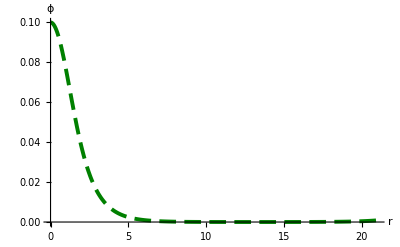
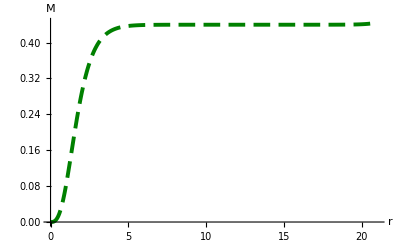

```mathematica
(*Algunos Plots*)
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];

ele={φ[r], M[r]};
eleLab={"ϕ", "M"};
Table[Plot[{Evaluate[ele[[i]]/.s]},{r,rMin,rMax},Background->White,PlotRange->{All, All},
AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]}],{i,2}]
```

La frecuancia física es, 1.1631

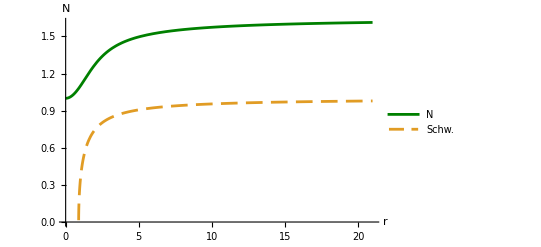
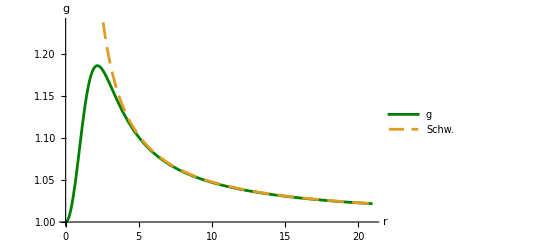

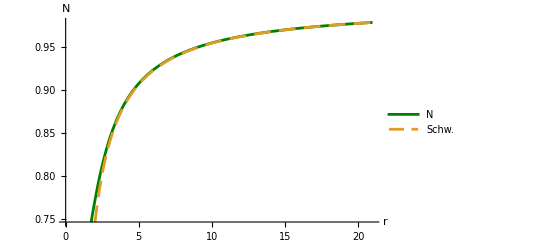
{-Graphics-,-Graphics-}

```mathematica
(* Ploteando la función NN y gg y checando que cumpla el comportamiento asintótico esperado *)
Masa=M[rMax]/.s;
Sch[r_,Masa_]:=Sqrt[(1-(2Masa)/r)];

(*Escalando N, y obteniendo w "física"*)
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
 w2=w*B[[1,1,1,2]];
Print["La frecuancia física es, ", w2]

ele={NN[r], gg[r]};
ele2={Sch[r,Masa], Sch[r,Masa]^-1};
eleLab={"N", "g"};
Table[Plot[{Evaluate[ele[[i]]/.s],ele2[[i]]},{r,rMin,rMax},PlotLegends->Placed[{eleLab[[i]],"Schw."},{0.85,0.56}],
Background->White,PlotRange->Automatic,AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]}],{i,2}]

(*Escalando N*)
ele={NN[r]*B[[1,1,1,2]], gg[r]};
Table[Plot[{Evaluate[ele[[i]]/.s],ele2[[i]]},{r,rMin,rMax},PlotLegends->Placed[{eleLab[[i]],"Schw."},{0.85,0.56}],
Background->White,PlotRange->Automatic,AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]}(*,AspectRatio->1*)],{i,2}]
```

```mathematica
"La frecuancia física es, "1.1633844520876777
```

#### estrella de neutrones

```mathematica
system2=system/.{epsil->0,den[r]->(pres[r]/k)^(1/Γ)+pres[r]/(Γ-1)}/.{ φ->Function[r,0]}/.{pres->P,m->1, Mp->1}(*TOV*)
```

{True,gg'[r]==(4 π (gg[r]/(8 π)+gg[r]^3 (-1/(8 π)+r^2 (P[r]/(-1+Γ)+(P[r]/k)^(1/Γ)))))/r,NN'[r]==(4 π NN[r] (-1/(8 π)+gg[r]^2 (1/(8 π)+r^2 P[r])))/r,P'[r]==-((P[r]+P[r]/(-1+Γ)+(P[r]/k)^(1/Γ)) NN'[r])/NN[r]}

```mathematica
(*near of origin*)
```

```mathematica
eq1=Numerator@Factor@(system2[[2,1]]-system2[[2,2]]);
eq2=Numerator@Factor@(system2[[3,1]]-system2[[3,2]]);

(*expandiendo*)
ser1=Series[Numerator[eq1],{r, 0,2}]//Factor//Normal;
ser2=Series[Numerator[eq2],{r, 0,2}]//Factor//Normal;
```

```mathematica
(*orden cero*)
ordeq10= Coefficient[ser1,r,0]//Simplify;
ordeq20= Coefficient[ser2,r,0]//Simplify;

(*orden 1*)
ordeq11= Coefficient[ser1,r,1]//Simplify;
ordeq21= Coefficient[ser2,r,1]//Simplify;
```

```mathematica
gg0=Last@Solve[ordeq10==0, gg[0]]
dg=Last@Solve[ordeq11==0/.gg0,gg'[0]]
dN=Last@Solve[ordeq21==0/.dg/.gg0,NN'[0]]
```

{gg[0]→1}

{gg'[0]→0}

{NN'[0]→0}

```mathematica
SNO=Series[NN[r],{r,0,1}]/.gg0/.dN/.dg//Normal
SgO=Series[gg[r],{r,0,1}]/.gg0/.dN/.dg//Normal
```

NN[0]

1

```mathematica
(*Resolviendo el sistema*)
```

```mathematica
ClearAll[rMin, Γ, k, p0,N0,P]
EqsList={};
BCList={};
CoefFunctionsList={};
```

```mathematica
AppendTo[CoefFunctionsList,{NN,gg, P}];
(*AppendTo[EqsList,{system2[[2]],system2[[3]],system2[[4]]}]*)
AppendTo[EqsList,{Evaluate[system2[[3,1]]]==If[P[r]>p0/10^4,Evaluate[system2[[3,2]]],Evaluate[system2[[3,2]]/.P->Function[r,0]]],Evaluate[system2[[2,1]]]==If[P[r]>p0/10^4,Evaluate[system2[[2,2]]],Evaluate[system2[[2,2]]/.P->Function[r,0]]],
Evaluate[system2[[4,1]]]==If[P[r]>p0/10^4,Evaluate[system2[[4,2]]],Evaluate[system2[[4,2]]/.P->Function[r,0]]]}]
AppendTo[BCList,{NN[rMin]==SNO,  gg[rMin] ==SgO, P[rMin] ==  p0}/.{NN[0]->N0,r->rMin}]
(*AppendTo[BCList,{NN[rMin]==SNO/.{NN[0]->N0,r->rMin},  gg[rMin] ==SgO/.{NN[0]->N0,r->rMin}, P[rMin] ==  p0,WhenEvent[P[r]==0,{rmax=r,Print[p[r]]};"StopIntegration" ]}]*)
```

{{NN'[r]==If[P[r]>p0/10000,(4 π NN[r] (-1/(8 π)+gg[r]^2 (1/(8 π)+r^2 P[r])))/r,(4 π (-1/(8 π)+gg[r]^2/(8 π)) NN[r])/r],gg'[r]==If[P[r]>p0/10000,(4 π (gg[r]/(8 π)+gg[r]^3 (-1/(8 π)+r^2 (P[r]/(-1+Γ)+(P[r]/k)^(1/Γ)))))/r,(4 π (gg[r]/(8 π)+(-1/(8 π)+0^(1/Γ) r^2) gg[r]^3))/r],P'[r]==If[P[r]>p0/10000,-((P[r]+P[r]/(-1+Γ)+(P[r]/k)^(1/Γ)) NN'[r])/NN[r],-(0^(1/Γ) NN'[r])/NN[r]]}}

{{NN[rMin]==N0,gg[rMin]==1,P[rMin]==p0}}

```mathematica
(*Ejemplo*)
rMin=10^-5;
rMax=20;(*6.65*)
p0=0.0025;
Γ= 2;
k= 100;
N0=1;

s=NDSolve[{EqsList[[1]],BCList[[1]]},CoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"},InterpolationOrder->All]
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],P→InterpolatingFunction[…]}}

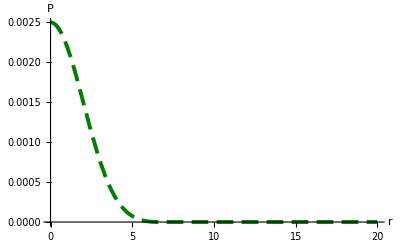
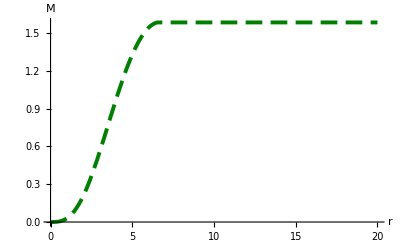

```mathematica
(*Algunos Plots*)
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];

ele={P[r], M[r]};
eleLab={"P", "M"};
Table[Plot[{Evaluate[ele[[i]]/.s]},{r,rMin,rMax},Background->White,PlotRange->{All, All},
AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]}],{i,2}]
```

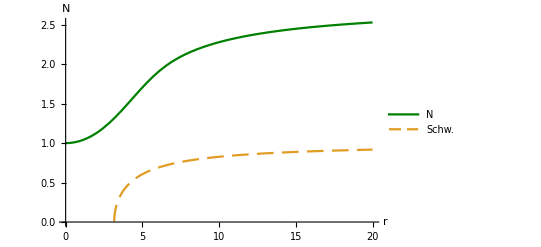
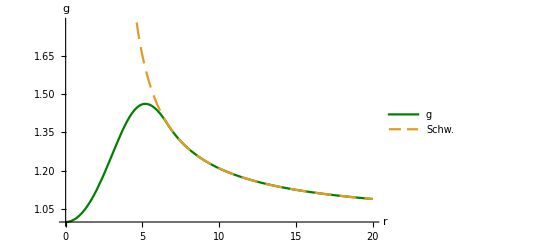

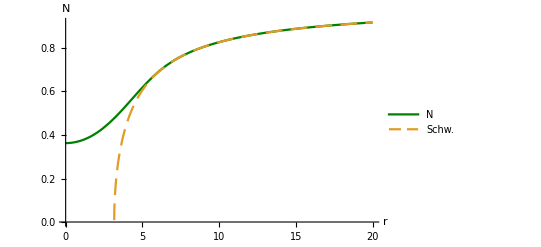
{-Graphics-,-Graphics-}

```mathematica
(* Ploteando la función NN y gg y checando que cumpla el comportamiento asintótico esperado *)
Masa=M[rMax]/.s;
Sch[r_,Masa_]:=Sqrt[(1-(2Masa)/r)];

(*Escalando N, y obteniendo w "física"*)
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];

ele={NN[r], gg[r]};
ele2={Sch[r,Masa], Sch[r,Masa]^-1};
eleLab={"N", "g"};
Table[Plot[{Evaluate[ele[[i]]/.s],ele2[[i]]},{r,rMin,rMax},PlotLegends->Placed[{eleLab[[i]],"Schw."},{0.85,0.56}],
Background->White,PlotRange->Automatic,AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]}],{i,2}]

(*Escalando N*)
ele={NN[r]*B[[1,1,1,2]], gg[r]};
Table[Plot[{Evaluate[ele[[i]]/.s],ele2[[i]]},{r,rMin,rMax},PlotLegends->Placed[{eleLab[[i]],"Schw."},{0.85,0.56}],
Background->White,PlotRange->Automatic,AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]}(*,AspectRatio->1*)],{i,2}]
```

#### estrella hibrida

```mathematica
system3=system/.{epsil->0,den[r]-> (pres[r]/k)^(1/Γ)+pres[r]/(Γ-1)}/.{pres-> P,m->1, Mp->1}
```

{φ''[r]==gg[r]^2 (2-w^2/NN[r]^2) φ[r]+(gg'[r] φ'[r])/gg[r]-((2 NN[r]+r NN'[r]) φ'[r])/(r NN[r]),gg'[r]==(4 π (gg[r]/(8 π)+gg[r]^3 (-1/(8 π)+r^2 (P[r]/(-1+Γ)+(P[r]/k)^(1/Γ)))))/r+(2 aB π r gg[r] (gg[r]^2 (w^2+2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/NN[r]^2,NN'[r]==(4 π NN[r] (-1/(8 π)+gg[r]^2 (1/(8 π)+r^2 P[r])))/r+(2 aB π r (gg[r]^2 (w^2-2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/NN[r],P'[r]==-((P[r]+P[r]/(-1+Γ)+(P[r]/k)^(1/Γ)) NN'[r])/NN[r]}

```mathematica
(*near of origin*)
eq1=Numerator@Factor@(system3[[1,1]]-system3[[1,2]]);
eq2=Numerator@Factor@(system3[[2,1]]-system3[[2,2]]);
eq3=Numerator@Factor@(system3[[3,1]]-system3[[3,2]]);

(*expandiendo*)
ser1=Series[Numerator[eq1],{r, 0,2}]//Factor//Normal;
ser2=Series[Numerator[eq2],{r, 0,2}]//Factor//Normal;
ser3=Series[Numerator[eq3],{r, 0,2}]//Factor//Normal;
```

```mathematica
(*orden cero*)
ordeq10= Coefficient[ser1,r,0]//Simplify;
ordeq20= Coefficient[ser2,r,0]//Simplify;
ordeq30= Coefficient[ser3,r,0]//Simplify;

(*orden 1*)
ordeq11= Coefficient[ser1,r,1]//Simplify;
ordeq21= Coefficient[ser2,r,1]//Simplify;
ordeq31= Coefficient[ser3,r,1]//Simplify;
```

```mathematica
dphi=Last@Solve[ordeq10==0,φ'[0]]
gg0=Last@Solve[ordeq20==0/.dphi,gg[0]]
ddphi=Last@Solve[ordeq11==0/.dphi/.gg0,φ''[0]]
dgg0=Last@Solve[ordeq21==0/.dphi/.gg0/.ddphi,gg'[0]]
dN=Last@Solve[ordeq31==0/.dphi/.gg0/.ddphi/.dgg0,NN'[0]]
```

{φ'[0]→0}

{gg[0]→1}

{φ''[0]→(-w^2 φ[0]+2 NN[0]^2 φ[0])/(3 NN[0]^2)}

{gg'[0]→0}

{NN'[0]→0}

```mathematica
SNO=Series[NN[r],{r,0,1}]/.dphi/.gg0/.ddphi/.dgg0/.dN//Normal
SgO=Series[gg[r],{r,0,1}]/.dphi/.gg0/.ddphi/.dgg0/.dN//Normal
SphiO=Series[ϕ[r],{r,0,2}]/.dphi/.gg0/.ddphi/.dgg0/.dN//Normal
```

NN[0]

1

φ[0]+(r^2 (-w^2 φ[0]+2 NN[0]^2 φ[0]))/(6 NN[0]^2)

```mathematica
(*Resolviendo el sistema*)
```

```mathematica
ClearAll[rMin, Γ, k, p0,N0,P, w,ϕ0]
EqsList={};
BCList={};
CoefFunctionsList={};
```

```mathematica
AppendTo[CoefFunctionsList,{NN,gg, ϕ,P}];
AppendTo[EqsList,{
Evaluate[system3[[3,1]]]==If[P[r]>p0/10^4,Evaluate[system3[[3,2]]],Evaluate[system3[[3,2]]/.P->Function[r,0]]],Evaluate[system3[[2,1]]]==If[P[r]>p0/10^4,Evaluate[system3[[2,2]]],Evaluate[system3[[2,2]]/.P->Function[r,0]]],
Evaluate[system3[[1,1]]]==If[P[r]>p0/10^4,Evaluate[system3[[1,2]]],Evaluate[system3[[1,2]]/.P->Function[r,0]]],
Evaluate[system3[[4,1]]]==If[P[r]>p0/10^4,Evaluate[system3[[4,2]]],Evaluate[system3[[4,2]]/.P->Function[r,0]]]}]
AppendTo[BCList,{NN[rMin]==SNO,  gg[rMin] ==SgO, ϕ[rMin]==SphiO ,ϕ'[rMin] ==0, P[rMin] ==  p0}/.{NN[0]->N0,φ[0]->ϕ0,r->rMin}]
```

{{NN'[r]==If[P[r]>p0/10000,(4 π NN[r] (-1/(8 π)+gg[r]^2 (1/(8 π)+r^2 P[r])))/r+(2 aB π r (gg[r]^2 (w^2-2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/NN[r],(4 π (-1/(8 π)+gg[r]^2/(8 π)) NN[r])/r+(2 aB π r (gg[r]^2 (w^2-2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/NN[r]],gg'[r]==If[P[r]>p0/10000,(4 π (gg[r]/(8 π)+gg[r]^3 (-1/(8 π)+r^2 (P[r]/(-1+Γ)+(P[r]/k)^(1/Γ)))))/r+(2 aB π r gg[r] (gg[r]^2 (w^2+2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/NN[r]^2,(4 π (gg[r]/(8 π)+(-1/(8 π)+0^(1/Γ) r^2) gg[r]^3))/r+(2 aB π r gg[r] (gg[r]^2 (w^2+2 NN[r]^2) φ[r]^2+NN[r]^2 φ'[r]^2))/NN[r]^2],φ''[r]==If[P[r]>p0/10000,gg[r]^2 (2-w^2/NN[r]^2) φ[r]+(gg'[r] φ'[r])/gg[r]-((2 NN[r]+r NN'[r]) φ'[r])/(r NN[r]),gg[r]^2 (2-w^2/NN[r]^2) φ[r]+(gg'[r] φ'[r])/gg[r]-((2 NN[r]+r NN'[r]) φ'[r])/(r NN[r])],P'[r]==If[P[r]>p0/10000,-((P[r]+P[r]/(-1+Γ)+(P[r]/k)^(1/Γ)) NN'[r])/NN[r],-(0^(1/Γ) NN'[r])/NN[r]]}}

{{NN[rMin]==N0,gg[rMin]==1,φ[rMin]==ϕ0+(rMin^2 (2 N0^2 ϕ0-w^2 ϕ0))/(6 N0^2),φ'[rMin]==0,P[rMin]==p0}}

```mathematica
(*Ejemplo*)
rMin=10^-5;
rMax=14;
p0=0.0025;
w=2.0600817;
ϕ0=0.1;
Γ= 2;
k= 100;
N0=1;
aB=1;

s=NDSolve[{EqsList[[1]],BCList[[1]]},CoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"},InterpolationOrder->All]
```

{{NN→InterpolatingFunction[…],gg→InterpolatingFunction[…],φ→InterpolatingFunction[…],P→InterpolatingFunction[…]}}

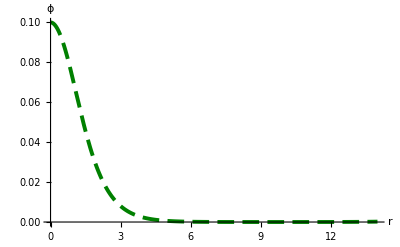
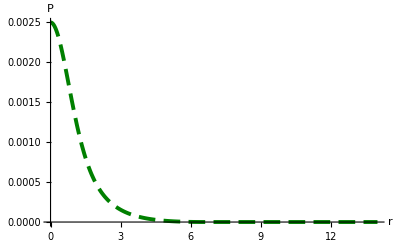
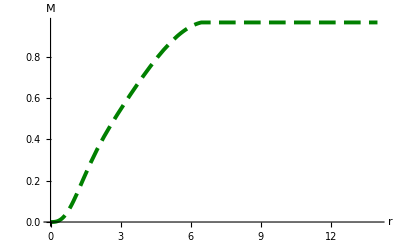

```mathematica
(*Algunos Plots*)
M[r_]:=Evaluate[1/2 r (1-1/gg[r]^2)];

ele={φ[r],P[r], M[r]};
eleLab={"ϕ","P", "M"};
Table[Plot[{Evaluate[ele[[i]]/.s]},{r,rMin,rMax},Background->White,PlotRange->{All, All},
AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]}],{i,3}]
```

La frecuancia física es, 0.870975

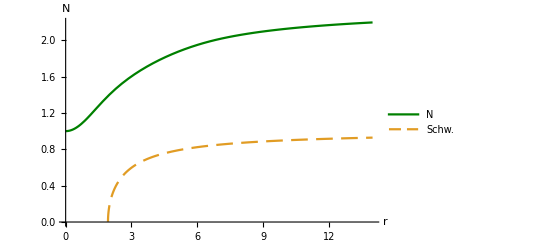
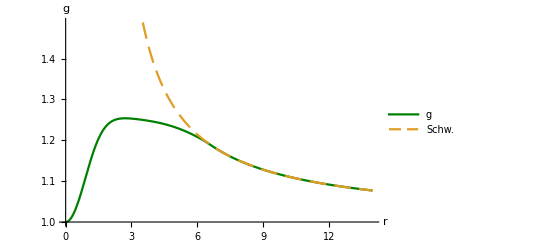

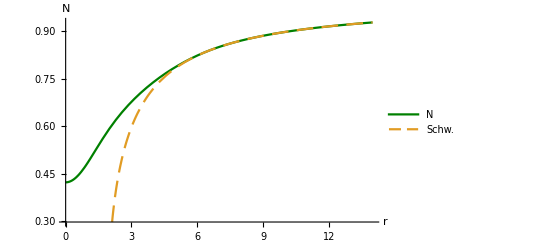
{-Graphics-,-Graphics-}

```mathematica
(* Ploteando la función NN y gg y checando que cumpla el comportamiento asintótico esperado *)
Masa=M[rMax]/.s;
Sch[r_,Masa_]:=Sqrt[(1-(2Masa)/r)];

(*Escalando N, y obteniendo w "física"*)
B=NumberForm[Solve[C*Evaluate[NN[rMax]/.s]*Evaluate[gg[rMax]/.s]==1,C],{18,17}];
 w2=w*B[[1,1,1,2]];
Print["La frecuancia física es, ", w2]

ele={NN[r], gg[r]};
ele2={Sch[r,Masa], Sch[r,Masa]^-1};
eleLab={"N", "g"};
Table[Plot[{Evaluate[ele[[i]]/.s],ele2[[i]]},{r,rMin,rMax},PlotLegends->Placed[{eleLab[[i]],"Schw."},{0.85,0.56}],
Background->White,PlotRange->Automatic,AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]}],{i,2}]

(*Escalando N*)
ele={NN[r]*B[[1,1,1,2]], gg[r]};
Table[Plot[{Evaluate[ele[[i]]/.s],ele2[[i]]},{r,rMin,rMax},PlotLegends->Placed[{eleLab[[i]],"Schw."},{0.85,0.56}],
Background->White,PlotRange->Automatic,AxesLabel->{"r",eleLab[[i]]},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]}(*,AspectRatio->1*)],{i,2}]
```